Funcion F(x)=(x/k)^2 --> Despejamos x --> x = k*u^(1/2)
Por lo que f(x)=dF(x)/dx = 2x/k^2

```mathematica
k=1;
```

```mathematica
RndPara[k_]:=k*Sqrt[RandomReal[]]
```

```mathematica
m[k_]:=Table[RndPara[k],100000];
```

```mathematica
muestras1=m[1];
```

Representamos para el caso de k = 1

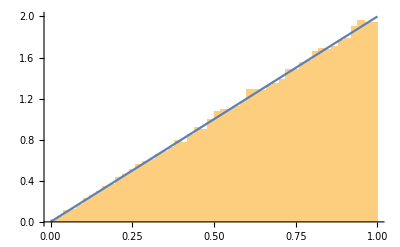

```mathematica
Show[Histogram[muestras1,50,PDF],Plot[(2*t)/(k^2),{t,0,1}]]
```

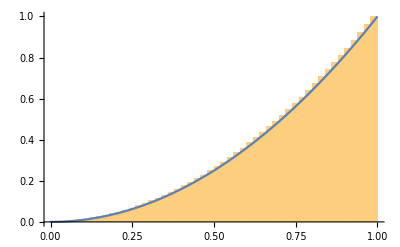

```mathematica
Show[Histogram[muestras1,50,CDF],Plot[(t/k)^2,{t,0,1}]]
```

Representamos para diferentes valores de K mediante Manipulate

```mathematica
Manipulate[Show[Plot[(2*t)/(k^2),{t,0,1}],Histogram[m[k],150,PDF]],{k,1,2,0.1}]
```

```mathematica
Manipulate[Show[Histogram[m[k],100,CDF],Plot[(t/k)^2,{t,0,k}]],{k,1,2,0.1}]
```